Part::partd: Part specification cx⟦2⟧ is longer than depth of object.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 0.01 Cos[1.84366+k3].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Part::partw: Part 2 of {{0,0,1.84366}} does not exist.

Part::partw: Part 3 of {{0,0,1.84366}}⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

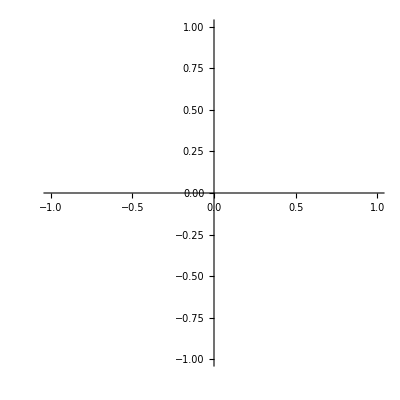
{{Null^3 -Graphics-},{□}}

```mathematica
{{fDrop[x_] := (
Block[{b=1.84366,c=-2.9},
Return[{
	     Cos[x[[3]]],
	     Sin[x[[3]]],
	     If[x[[1]]==0&&x[[2]]==0,b,2b+cx[[2]]-Sin[x[[3]]]/x[[1]]]
}]
]
);

AB4Drop[f_,y0_,h_] := (
Block[{y,fVal,i,k1,k2,k3,k4},
y = {y0};
fVal = {};
i = 1;
While[i<=3,
AppendTo[fVal,f[y[[i]]]];
k1 = N[h fVal[[i]]];
k2 = N[h f[y[[i]]+0.5k1]];
k3 = N[h f[y[[i]]+k3]];
k4 = N[h f[y[[i]]+k3]];
AppendTo[y,N[y[[i]]+(1.0/6.0)(k1+2k2+2k3+k4)]];
++i;
];
While[y[[i-1,1]]<1,
AppendTo[fVal,f[y[[i]]]];
AppendTo[y,y[[i]]+(h/24) (55 fVal[[i]] - 59fVal[[i-1]] + 37fVal[[i-2]] - 9fVal[[i-3]])];
++i;
];
Table[{(i-1)h,y[[i]]},{i,1,Length[y]}]
]
);

dropRes = AB4Drop[fDrop,{0,0,1.84366},0.01];
ListLinePlot[
Table[{dropRes[[i,2,1]],dropRes[[i,2,2]]},{i,1,Length[dropRes]}],
AspectRatio -> Automatic
]}, {□}}
```